```mathematica
(*INTEGRAL EXACTA 1 PARA EQ DE EVOLUCION DE LAS TEMPERATURAS HORIZONTALES T_XY*)
Integrate[(1+b (Cos[x])^2)^(3/2)(Sin[x])^3,{x,0,Pi},Assumptions->b>0]
```

(-6 √(b (1+b))+32 √(b^3 (1+b))+8 √(b^5 (1+b))+6 (1+6 b) ArcSinh[√b])/(48 b^(3/2))

```mathematica
Simplify[(-6 √(b (1+b))+32 √(b^3 (1+b))+8 √(b^5 (1+b))+6 (1+6 b) ArcSinh[√b])/(48 b^(3/2))]
```

(-6 √(b (1+b))+32 √(b^3 (1+b))+8 √(b^5 (1+b))+6 (1+6 b) ArcSinh[√b])/(48 b^(3/2))

```mathematica
Series[(-6 √(b (1+b))+32 √(b^3 (1+b))+8 √(b^5 (1+b))+6 (1+6 b) ArcSinh[√b])/(48 b^(3/2)),{b,0,4}]
```

(2 (b^(3/2)+√(b^3)))/(3 b^(3/2))+((-3 b^(5/2)+10 b √(b^3)+5 √(b^5)) b)/(30 b^(5/2))+((18 b^(5/2)-35 b √(b^3)+35 √(b^5)) b^2)/(420 b^(5/2))+((-25 b^(5/2)+42 b √(b^3)-21 √(b^5)) b^3)/(1008 b^(5/2))+((35 b^(5/2)-55 b √(b^3)+22 √(b^5)) b^4)/(2112 b^(5/2))+O[b]^5

```mathematica
(*INTEGRAL EXACTA 2 PARA EQ DE EVOLUCION DE LAS TEMPERATURAS HORIZONTALES T_XY*)
```

```mathematica
Integrate[(1+b (Cos[x])^2)(Sin[x])^3,{x,0,Pi},Assumptions->b>0]
```

(4 (5+b))/15

```mathematica
Series[(-√(b (1+b))+2 √(b^3 (1+b))+(1+4 b) ArcSinh[√b])/(4 b^(3/2)),{b,0,4}]
```

(5 b^(3/2)+3 √(b^3))/(6 b^(3/2))+((-7 b^(3/2)+15 √(b^3)) b)/(60 b^(3/2))+((27 b^(3/2)-35 √(b^3)) b^2)/(560 b^(3/2))+((-55 b^(3/2)+63 √(b^3)) b^3)/(2016 b^(3/2))-(5 (-91 b^(3/2)+99 √(b^3)) b^4)/(25344 b^(3/2))+O[b]^5

```mathematica
(*INTEGRAL EXACTA 3 PARA EQ DE EVOLUCION DE LAS TEMPERATURAS HORIZONTALES T_XY*)
```

```mathematica
Integrate[(1+b (Sin[x])^2)^(3/2)(Cos[x])^3,x,Assumptions->b>0]
```

1/(48 b^(3/2))(3 (1+6 b) ArcSinh[√b Sin[x]]+√b Sin[x] √(1+b Sin[x]^2) (-3+30 b+2 b (-7+6 b) Sin[x]^2-8 b^2 Sin[x]^4))

```mathematica
FullSimplify[1/(48 b^(3/2))(3 (1+6 b) ArcSinh[√b Sin[x]]+√b Sin[x] √(1+b Sin[x]^2) (-3+30 b+2 b (-7+6 b) Sin[x]^2-8 b^2 Sin[x]^4))]
```

```mathematica
1/(48 b^(3/2))(3 (1+6 b) ArcSinh[√b Sin[0]]+√b Sin[0] √(1+b Sin[0]^2) (-3+30 b+2 b (-7+4 b+2 b Cos[2 0]) Sin[0]^2))
```

0

```mathematica
Integrate[2*(1+b (Sin[x])^2/2)(Cos[x])^3,x,Assumptions->b>0]
```

(3 Sin[x])/2+1/8 b Sin[x]+1/6 Sin[3 x]-1/48 b Sin[3 x]-1/80 b Sin[5 x]

```mathematica
(3 Sin[ArcSin[x]])/2+1/8 b Sin[ArcSin[x]]+1/6 Sin[3 ArcSin[x]]-1/48 b Sin[3 ArcSin[x]]-1/80 b Sin[5 ArcSin[x]]
```

(3 x)/2+(b x)/8+1/6 Sin[3 ArcSin[x]]-1/48 b Sin[3 ArcSin[x]]-1/80 b Sin[5 ArcSin[x]]

```mathematica
Simplify[(3 x)/2+(b x)/8+1/6 Sin[3 ArcSin[x]]-1/48 b Sin[3 ArcSin[x]]-1/80 b Sin[5 ArcSin[x]]]
```

2 x+1/3 (-2+b) x^3-(b x^5)/5

```mathematica
(3 Sin[x])/2+3/8 b Sin[x]+1/6 Sin[3 x]-1/16 b Sin[3 x]-3/80 b Sin[5 x]
(3 Sin[ArcSin[x]])/2+3/8 b Sin[ArcSin[x]]+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]
```

(3 Sin[x])/2+3/8 b Sin[x]+1/6 Sin[3 x]-1/16 b Sin[3 x]-3/80 b Sin[5 x]

(3 x)/2+(3 b x)/8+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]

```mathematica
Simplify[(3 x)/2+(3 b x)/8+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]]
```

2 x+(-2/3+b) x^3-(3 b x^5)/5

```mathematica
Integrate[2*(1+3*b (Sin[x])^2/2)(Cos[x])^3,x,Assumptions->b>0]
```

```mathematica
(3 Sin[ArcSin[x]])/2+3/8 b Sin[ArcSin[x]]+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]
```

(3 x)/2+(3 b x)/8+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]

```mathematica
Simplify[(3 x)/2+(3 b x)/8+1/6 Sin[3 ArcSin[x]]-1/16 b Sin[3 ArcSin[x]]-3/80 b Sin[5 ArcSin[x]]]
```

2 x+(-2/3+b) x^3-(3 b x^5)/5

```mathematica
Integrate[2 x+(-2/3+b) x^3-(3 b x^5)/5,{x,0,1},Assumptions->b>0]
```

1+1/4 (-2/3+b)-b/10

```mathematica
Simplify[1+1/4 (-2/3+b)-b/10]
```

5/6+(3 b)/20

```mathematica
Simplify[1/4+1/64 (-2/3+b)-b/640]
```

23/96+(9 b)/640

```mathematica
Integrate[2 x+1/3 (-2+b) x^3-(b x^5)/5,{x,0,1},Assumptions->b>0]
```

1+1/12 (-2+b)-b/30

```mathematica
Simplify[1+1/12 (-2+b)-b/30]
```

5/6+b/20

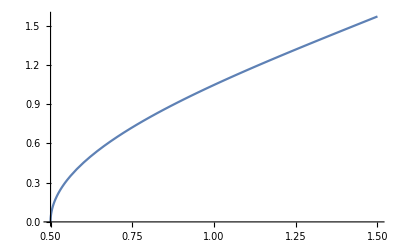

```mathematica
Plot[Pi/2-ArcSin[3/2-z],{z,1/2,3/2}]
```

```mathematica
Integrate[(1+b (Sin[x])^2/2)(Cos[x])^3,x,Assumptions->b>0]
```

```mathematica
(3 Sin[ArcSin[H-1/2-x]])/4+1/16 b Sin[ArcSin[H-1/2-x]]+1/12 Sin[3 ArcSin[H-1/2-x]]-1/96 b Sin[3 ArcSin[H-1/2-x]]-1/160 b Sin[5 ArcSin[H-1/2-x]]
```

3/4 (-1/2+H-x)+1/16 b (-1/2+H-x)-1/12 Sin[3 ArcSin[1/2-H+x]]+1/96 b Sin[3 ArcSin[1/2-H+x]]+1/160 b Sin[5 ArcSin[1/2-H+x]]

```mathematica
Simplify[3/4 (-1/2+H-x)+1/16 b (-1/2+H-x)-1/12 Sin[3 ArcSin[1/2-H+x]]+1/96 b Sin[3 ArcSin[1/2-H+x]]+1/160 b Sin[5 ArcSin[1/2-H+x]]]
```

1/480 (15 (12+b) (-1+2 H-2 x)+5 (-8+b) Sin[3 ArcSin[1/2-H+x]]+3 b Sin[5 ArcSin[1/2-H+x]])

```mathematica
TrigReduce[1/480 (15 (12+b) (-1+2 H-2 x)+5 (-8+b) Sin[3 ArcSin[1/2-H+x]]+3 b Sin[5 ArcSin[1/2-H+x]])]
```

1/480 (-180-15 b+360 H+30 b H-360 x-30 b x-40 Sin[3 ArcSin[1/2-H+x]]+5 b Sin[3 ArcSin[1/2-H+x]]+3 b Sin[5 ArcSin[1/2-H+x]])

```mathematica
Integrate[1/480 (15 (12+b) (-1+2 H-2 x)+5 (-8+b) Sin[3 ArcSin[1/2-H+x]]+3 b Sin[5 ArcSin[1/2-H+x]]),{x,H-3/2,H-1/2},Assumptions->H>0]
```

5/12+b/40

```mathematica
(3 Sin[ArcSin[3/2-x]])/4+1/16 b Sin[ArcSin[3/2-x]]+1/12 Sin[3ArcSin[3/2-x]]-1/96 b Sin[3 ArcSin[3/2-x]]-1/160 b Sin[5 ArcSin[3/2-x]]
```

3/4 (3/2-x)+1/16 b (3/2-x)+1/12 Sin[3 ArcSin[3/2-x]]-1/96 b Sin[3 ArcSin[3/2-x]]-1/160 b Sin[5 ArcSin[3/2-x]]

```mathematica
Simplify[3/4 (3/2-x)+1/16 b (3/2-x)+1/12 Sin[3 ArcSin[3/2-x]]-1/96 b Sin[3 ArcSin[3/2-x]]-1/160 b Sin[5 ArcSin[3/2-x]]]
```

1/480 (-15 (12+b) (-3+2 x)-5 (-8+b) Sin[3 ArcSin[3/2-x]]-3 b Sin[5 ArcSin[3/2-x]])

```mathematica
Integrate[1/480 (-15 (12+b) (-3+2 x)-5 (-8+b) Sin[3 ArcSin[3/2-x]]-3 b Sin[5 ArcSin[3/2-x]]),{x,1/2,3/2}]
```

5/12+b/40

```mathematica
(3 Sin[ArcSin[(x-1/2)]])/4+1/16 b Sin[ArcSin[(x-1/2)]]+1/12 Sin[3 ArcSin[(x-1/2)]]-1/96 b Sin[3 ArcSin[(x-1/2)]]-1/160 b Sin[5 ArcSin[(x-1/2)]]
```

3/4 (-1/2+x)+1/16 b (-1/2+x)-1/12 Sin[3 ArcSin[1/2-x]]+1/96 b Sin[3 ArcSin[1/2-x]]+1/160 b Sin[5 ArcSin[1/2-x]]

```mathematica
Simplify[3/4 (-1/2+x)+1/16 b (-1/2+x)-1/12 Sin[3 ArcSin[1/2-x]]+1/96 b Sin[3 ArcSin[1/2-x]]+1/160 b Sin[5 ArcSin[1/2-x]]]
```

```mathematica
Integrate[1/480 (15 (12+b) (-1+2 x)+5 (-8+b) Sin[3 ArcSin[1/2-x]]+3 b Sin[5 ArcSin[1/2-x]]),{x,1/2,3/2}]
```

5/12+b/40

```mathematica
Integrate[(1+3*b (Sin[x])^2/2)(Cos[x])^3,x,Assumptions->b>0]
```

(3 Sin[x])/4+3/16 b Sin[x]+1/12 Sin[3 x]-1/32 b Sin[3 x]-3/160 b Sin[5 x]

```mathematica
(3 Sin[ArcSin[H-1/2-x]])/4+3/16 b Sin[ArcSin[H-1/2-x]]+1/12 Sin[3 ArcSin[H-1/2-x]]-1/32 b Sin[3 ArcSin[H-1/2-x]]-3/160 b Sin[5 ArcSin[H-1/2-x]]
```

3/4 (-1/2+H-x)+3/16 b (-1/2+H-x)-1/12 Sin[3 ArcSin[1/2-H+x]]+1/32 b Sin[3 ArcSin[1/2-H+x]]+3/160 b Sin[5 ArcSin[1/2-H+x]]

```mathematica
Simplify[3/4 (-1/2+H-x)+3/16 b (-1/2+H-x)-1/12 Sin[3 ArcSin[1/2-H+x]]+1/32 b Sin[3 ArcSin[1/2-H+x]]+3/160 b Sin[5 ArcSin[1/2-H+x]]]
```

1/480 (45 (4+b) (-1+2 H-2 x)+5 (-8+3 b) Sin[3 ArcSin[1/2-H+x]]+9 b Sin[5 ArcSin[1/2-H+x]])

```mathematica
TrigReduce[1/480 (45 (4+b) (-1+2 H-2 x)+5 (-8+3 b) Sin[3 ArcSin[1/2-H+x]]+9 b Sin[5 ArcSin[1/2-H+x]])]
```

1/480 (-180-45 b+360 H+90 b H-360 x-90 b x-40 Sin[3 ArcSin[1/2-H+x]]+15 b Sin[3 ArcSin[1/2-H+x]]+9 b Sin[5 ArcSin[1/2-H+x]])

```mathematica
Integrate[1/480 (45 (4+b) (-1+2 H-2 x)+5 (-8+3 b) Sin[3 ArcSin[1/2-H+x]]+9 b Sin[5 ArcSin[1/2-H+x]]),{x,H-3/2,H-1/2},Assumptions->H>0]
```

5/12+(3 b)/40

```mathematica
Integrate[(1+b (Cos[x])^2)(Sin[x])^(d-2)Cos[x]^2,{x,0,Pi},Assumptions->b>0 && Element[d,Integers] && d≥ 2]
```

((2+3 b+d) √π Gamma[1/2 (-1+d)])/(4 Gamma[2+d/2])

```mathematica
Integrate[(1+b (Sin[x])^2)(Cos[x])^2,x,Assumptions->b>0  ]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.

Integrate[1,0,Assumptions→b>0]

```mathematica
Integrate[2(1+b (Sin[x])^2)(Cos[x])^d,x,Assumptions->b>0 && Element[d,Integers] && d≥ 2 ]
```

1/2 (-(ⅈ 2^-d b ⅇ^(-2 ⅈ x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^d (1+ⅇ^(2 ⅈ x)) ((2+d) ⅇ^(4 ⅈ x) Hypergeometric2F1[1,2+d/2,2-d/2,-ⅇ^(2 ⅈ x)]+(-2+d) Hypergeometric2F1[1,d/2,-d/2,-ⅇ^(2 ⅈ x)]))/(-4+d^2)-(4 Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d)-(2 b Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d))

```mathematica
Simplify[%2]
```

-(ⅈ 2^(-1-d) b ⅇ^(-2 ⅈ x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^d (1+ⅇ^(2 ⅈ x)) ((2+d) ⅇ^(4 ⅈ x) Hypergeometric2F1[1,2+d/2,2-d/2,-ⅇ^(2 ⅈ x)]+(-2+d) Hypergeometric2F1[1,d/2,-d/2,-ⅇ^(2 ⅈ x)]))/(-4+d^2)-(2 Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d)-(b Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d)

```mathematica
f[x_,d_] := -(ⅈ 2^(-1-d) b ⅇ^(-2 ⅈ x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^d (1+ⅇ^(2 ⅈ x)) ((2+d) ⅇ^(4 ⅈ x) Hypergeometric2F1[1,2+d/2,2-d/2,-ⅇ^(2 ⅈ x)]+(-2+d) Hypergeometric2F1[1,d/2,-d/2,-ⅇ^(2 ⅈ x)]))/(-4+d^2)-(2 Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d)-(b Cos[x]^(1+d) Csc[x] Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Cos[x]^2] √(Sin[x]^2))/(1+d)

f[0,3]



Integrate[(1+b (x)^2)(1-x^2)^((d-1)/2)x^2,x,Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 b ComplexInfinity encountered.

Indeterminate

1/3 x^3 Hypergeometric2F1[3/2,(1-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(1-d)/2,7/2,x^2]

```mathematica
f[x_]:=(3 Sin[x])/2+1/4 b Sin[x]+1/6 Sin[3 x]-1/24 b Sin[3 x]-1/40 b Sin[5 x]
f[0]

g[x_]:= x+(b x)/4+1/2 Sin[2 x]-1/16 b Sin[4 x]
g[ArcSin[z]]
```

0

ArcSin[z]+1/4 b ArcSin[z]+1/2 Sin[2 ArcSin[z]]-1/16 b Sin[4 ArcSin[z]]

```mathematica
Simplify[ArcSin[z]+1/4 b ArcSin[z]+1/2 Sin[2 ArcSin[z]]-1/16 b Sin[4 ArcSin[z]]]
```

1/4 (4+b) ArcSin[z]-1/8 (-4+b Cos[2 ArcSin[z]]) Sin[2 ArcSin[z]]

(3 Sin[x])/2+1/4 b Sin[x]+1/6 Sin[3 x]-1/24 b Sin[3 x]-1/40 b Sin[5 x]

```mathematica
1/2 (-1/(-4+Integer^2)ⅈ 2^-Integer b ⅇ^(-2 ⅈ x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^Integer (1+ⅇ^(2 ⅈ x)) (ⅇ^(4 ⅈ x) (2+Integer) Hypergeometric2F1[1,2+Integer/2,2-Integer/2,-ⅇ^(2 ⅈ x)]+(-2+Integer) Hypergeometric2F1[1,Integer/2,-Integer/2,-ⅇ^(2 ⅈ x)])-(4 Cos[x]^(1+Integer) Csc[x] Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,Cos[x]^2] √(Sin[x]^2))/(1+Integer)-(2 b Cos[x]^(1+Integer) Csc[x] Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,Cos[x]^2] √(Sin[x]^2))/(1+Integer))
f[x_] := 1/2 (-1/(-4+Integer^2)ⅈ 2^-Integer b ⅇ^(-2 ⅈ x) (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^Integer (1+ⅇ^(2 ⅈ x)) (ⅇ^(4 ⅈ x) (2+Integer) Hypergeometric2F1[1,2+Integer/2,2-Integer/2,-ⅇ^(2 ⅈ x)]+(-2+Integer) Hypergeometric2F1[1,Integer/2,-Integer/2,-ⅇ^(2 ⅈ x)])-(4 Cos[x]^(1+Integer) Csc[x] Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,Cos[x]^2] √(Sin[x]^2))/(1+Integer)-(2 b Cos[x]^(1+Integer) Csc[x] Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,Cos[x]^2] √(Sin[x]^2))/(1+Integer))
```

Infinity::indet: Indeterminate expression (0 √π ComplexInfinity Gamma[3/2+Integer/2])/((1+Integer) Gamma[1+Integer/2]) encountered.

Infinity::indet: Indeterminate expression (0 b √π ComplexInfinity Gamma[3/2+Integer/2])/((1+Integer) Gamma[1+Integer/2]) encountered.

Indeterminate

```mathematica
f[ArcSin[z]]
```

1/2 (-(4 √(z^2) (1-z^2)^((1+Integer)/2) Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,1-z^2])/((1+Integer) z)-(2 b √(z^2) (1-z^2)^((1+Integer)/2) Hypergeometric2F1[1/2,(1+Integer)/2,(3+Integer)/2,1-z^2])/((1+Integer) z)-1/(-4+Integer^2)ⅈ 2^-Integer b ⅇ^(-2 ⅈ ArcSin[z]) (ⅇ^(-ⅈ ArcSin[z])+ⅇ^(ⅈ ArcSin[z]))^Integer (1+ⅇ^(2 ⅈ ArcSin[z])) (ⅇ^(4 ⅈ ArcSin[z]) (2+Integer) Hypergeometric2F1[1,2+Integer/2,2-Integer/2,-ⅇ^(2 ⅈ ArcSin[z])]+(-2+Integer) Hypergeometric2F1[1,Integer/2,-Integer/2,-ⅇ^(2 ⅈ ArcSin[z])]))

Infinity::indet: Indeterminate expression (0 √π ComplexInfinity Gamma[3/2+Integer/2])/((1+Integer) Gamma[1+Integer/2]) encountered.

Infinity::indet: Indeterminate expression (0 b √π ComplexInfinity Gamma[3/2+Integer/2])/((1+Integer) Gamma[1+Integer/2]) encountered.

Sequence[Indeterminate,0]

```mathematica
Integrate[(1+b (Sin[x])^2/2)(Cos[x])^3,x,Assumptions->b>0]
```

(3 Sin[x])/4+1/16 b Sin[x]+1/12 Sin[3 x]-1/96 b Sin[3 x]-1/160 b Sin[5 x]

```mathematica
Integrate[Sin[x]^4,x]
```

(3 x)/8-1/4 Sin[2 x]+1/32 Sin[4 x]

```mathematica
Integrate[Sin[x]^2,x]
```

x/2-1/4 Sin[2 x]

```mathematica
(x/2-1/4 Sin[2 x])^2
```

(x/2-1/4 Sin[2 x])^2

```mathematica
Simplify[(x/2-1/4 Sin[2 x])^2]
```

1/16 (-2 x+Sin[2 x])^2

```mathematica
Sin[2 ArcSin[x]]
```

Sin[2 ArcSin[x]]

```mathematica
Integrate[(1+b (x)^2)(1-x^2)^((d-3)/2)x^2,x,Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

1/3 x^3 Hypergeometric2F1[3/2,(3-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(3-d)/2,7/2,x^2]

```mathematica
1/3 x^3 Hypergeometric2F1[3/2,(1-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(1-d)/2,7/2,x^2]
f[x_]:=1/3 x^3 Hypergeometric2F1[3/2,(1-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(1-d)/2,7/2,x^2]
```

1/3 x^3 Hypergeometric2F1[3/2,(1-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(1-d)/2,7/2,x^2]

```mathematica
f[d_]:=1/3 x^3 Hypergeometric2F1[3/2,(1-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(1-d)/2,7/2,x^2]
```

```mathematica
f[0,2]
```

```mathematica
f[3]
```

1/35 b x^5 (7-5 x^2)+1/15 x^3 (5-3 x^2)

```mathematica
f[2]
```

1/3 x^3 (1-x^2)^(3/2) (3/(4 (1-x^2))+(3 (-2 x^2+(2 x ArcSin[x])/(√(1-x^2))))/(16 x^4 (1-x^2)))+1/5 b x^5 (1-x^2)^(3/2) (5/(6 (1-x^2))+(5 (-2 x^2-(4 x^4)/3+(2 x ArcSin[x])/(√(1-x^2))))/(32 x^6 (1-x^2)))

```mathematica
Simplify[1/3 x^3 (1-x^2)^(3/2) (3/(4 (1-x^2))+(3 (-2 x^2+(2 x ArcSin[x])/(√(1-x^2))))/(16 x^4 (1-x^2)))+1/5 b x^5 (1-x^2)^(3/2) (5/(6 (1-x^2))+(5 (-2 x^2-(4 x^4)/3+(2 x ArcSin[x])/(√(1-x^2))))/(32 x^6 (1-x^2)))]
```

1/48 (x √(1-x^2) (-6+12 x^2+b (-3-2 x^2+8 x^4))+3 (2+b) ArcSin[x])

```mathematica
∫1/48 (x √(1-x^2) (-6+12 x^2+b (-3-2 x^2+8 x^4))+3 (2+b) ArcSin[x])ⅆx
```

1/48 (1/35 √(1-x^2) (14 (16-7 x^2+6 x^4)+b (128-41 x^2-22 x^4+40 x^6))+3 (2+b) x ArcSin[x])

```mathematica
Integrate[1/48 (x √(1-x^2) (-6+12 x^2+b (-3-2 x^2+8 x^4))+3 (2+b) ArcSin[x]),{x,0,1}, Assumptions->b>0]
```

-2/15+b (-8/105+π/32)+π/16

```mathematica
f[x_]:=1/48 (1/35 √(1-x^2) (14 (16-7 x^2+6 x^4)+b (128-41 x^2-22 x^4+40 x^6))+3 (2+b) x ArcSin[x])
```

```mathematica
f[0]
```

```mathematica
(224+128 b)/1680
```

```mathematica
Integrate[1/3 x^3 Hypergeometric2F1[3/2,(3-d)/2,5/2,x^2]+1/5 b x^5 Hypergeometric2F1[5/2,(3-d)/2,7/2,x^2],{x,0,1},Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

```mathematica
(*INTEGRAL APROX  PARA EQ DE EVOLUCION DE LA TEMPERATURA Vertical T_z*)
```

```mathematica
-(2 (3+4 b+d))/((3+d) (-1+d^2))+(π^(3/2) (-2/Gamma[1+d/2]-(3 b)/Gamma[2+d/2]) Sec[(d π)/2])/(8 Gamma[3/2-d/2])

Integrate[(1+b (Cos[x])^2)(Sin[x])^(d-2)Cos[x]^2,{x,0,Pi},Assumptions->b>0 && Element[d,Integers]&& d≥ 2]


Integrate[(1+b (Cos[x])^2)(Sin[x])^d,x,Assumptions->b>0 && Element[d,Integers]&& d≥ 2]
```

```mathematica
(√(Cos[x]^2) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,Sin[x]^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Sin[x]^2]) Sec[x] Sin[x]^(1+d))/(1+d)

f[x_]:=(√(Cos[x]^2) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,Sin[x]^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Sin[x]^2]) Sec[x] Sin[x]^(1+d))/(1+d)
f[0]

f[ArcSin[z]]
```

(√(Cos[x]^2) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,Sin[x]^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,Sin[x]^2]) Sec[x] Sin[x]^(1+d))/(1+d)

(0^(1+d) (1+b))/(1+d)

(z^(1+d) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,z^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,z^2]))/(1+d)

```mathematica
(z^(1+d) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,z^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,z^2]))/(1+d)

Integrate[(z^(1+d) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,z^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,z^2]))/(1+d),{z,0,1},Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

(z^(1+d) (b Hypergeometric2F1[-1/2,(1+d)/2,(3+d)/2,z^2]+Hypergeometric2F1[1/2,(1+d)/2,(3+d)/2,z^2]))/(1+d)

```mathematica
(2^d (-Gamma[1+d/2]^2+Gamma[(1+d)/2] Gamma[(3+d)/2]))/Gamma[2+d]+1/4 b √π (Gamma[(1+d)/2]/Gamma[2+d/2]-Gamma[1+d/2]/Gamma[(5+d)/2])


g[d_]:=(2^d (-Gamma[1+d/2]^2+Gamma[(1+d)/2] Gamma[(3+d)/2]))/Gamma[2+d]+1/4 b √π (Gamma[(1+d)/2]/Gamma[2+d/2]-Gamma[1+d/2]/Gamma[(5+d)/2])
```

```mathematica
g[3]


(2^d (-Gamma[1+d/2]^2+Gamma[(1+d)/2] Gamma[(3+d)/2]))/Gamma[2+d]+1/4 b √π (Gamma[(1+d)/2]/Gamma[2+d/2]-Gamma[1+d/2]/Gamma[(5+d)/2])
```

1/3 (2-(9 π)/16)+1/4 b (8/(15 √π)-(√π)/8) √π

```mathematica
Simplify[1/3 (2-(9 π)/16)+1/4 b (8/(15 √π)-(√π)/8) √π]
```

1/480 (320+b (64-15 π)-90 π)

```mathematica
Integrate[(1+b (x)^2)(1-x^2)^((d-1)/2),x,Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

```mathematica
(x (-b (1-x^2)^((1+d)/2)+(2+b+d) Hypergeometric2F1[1/2,(1-d)/2,3/2,x^2]))/(2+d)


f[x_]:=(x (-b (1-x^2)^((1+d)/2)+(2+b+d) Hypergeometric2F1[1/2,(1-d)/2,3/2,x^2]))/(2+d)
```

```mathematica
f[0]
```

0

```mathematica
(x (-b (1-x^2)^((1+d)/2)+(2+b+d) Hypergeometric2F1[1/2,(1-d)/2,3/2,x^2]))/(2+d)
Integrate[(1+b (x)^2)(1-x^2),x,Assumptions->b>0 ]
```

(x (-b (1-x^2)^((1+d)/2)+(2+b+d) Hypergeometric2F1[1/2,(1-d)/2,3/2,x^2]))/(2+d)

```mathematica
x-1/3 (1-b) x^3-(b x^5)/5

Integrate[x-1/3 (1-b) x^3-(b x^5)/5,{x,0,1},Assumptions->b>0 ]
```

x-1/3 (1-b) x^3-(b x^5)/5

1/2+1/12 (-1+b)-b/30

```mathematica
Simplify[1/2+1/12 (-1+b)-b/30]
```

1/60 (25+3 b)

```mathematica
Integrate[(x (-b (1-x^2)^((1+d)/2)+(2+b+d) Hypergeometric2F1[1/2,(1-d)/2,3/2,x^2]))/(2+d),{x,0,1},Assumptions->b>0 &&Element[d,Integers]&&  d≥ 2]
```

-(3+2 b+d)/(3+4 d+d^2)+((2+b+d) π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2])

```mathematica
(*INTEGRAL APROX  PARA EQ DE EVOLUCION DE LAS TEMPERATURAS HORIZONTALES T*)
-(3+2 b+d)/(3+4 d+d^2)+((2+b+d) π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2])


f[d_] := -(3+2 b+d)/(3+4 d+d^2)+((2+b+d) π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2])


f[3]
```

-(3+2 b+d)/(3+4 d+d^2)+((2+b+d) π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2])

Infinity::indet: Indeterminate expression 0 (5+b) π^(3/2) ComplexInfinity encountered.

Indeterminate

```mathematica
Integrate[(1+b (Cos[x])^2)(Sin[x])^d,{x,0,Pi},Assumptions->b>0 && Element[d,Integers]&& d≥ 2]
```

```mathematica
(*INTEGRAL APROX  PARA EQ DE EVOLUCION DE LAS TEMPERATURAS HORIZONTALES T*)

((2+b+d) √π Gamma[(1+d)/2])/(2 Gamma[2+d/2])
```

```mathematica
Integrate[(1+b (Cos[x])^2)(Sin[x])^d,{x,0,Pi},Assumptions->b>0 && Element[d,Integers],&& d≥ 2]
```

```mathematica
f[d_]:= ((2+3 b+d) √π Gamma[1/2 (-1+d)])/(4 Gamma[2+d/2])
```

```mathematica
f[3]
```

2/15 (5+3 b)

```mathematica
Simplify[2/15 (5+3 b)]
```

2/3+(2 b)/5

```mathematica
Integrate[(1+b (Cos[x])^2)Sin[x]Cos[x]^2,{x,0,Pi},Assumptions->b>0 && Element[d,Integers]&& d≥ 2]
```

2/3+(2 b)/5

```mathematica
g[d_]:=(-(3+d)/(3+4 d+d^2)+((2+d) π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2]))((√π Gamma[(1+d)/2])/(4 Gamma[2+d/2]))^(-1)
```

```mathematica
Limit[g[d],d->3]
```

25/8

```mathematica
h[d_]:=(-2/(3+4 d+d^2)+(π^(3/2) Sec[(d π)/2])/(4 Gamma[1/2-d/2] Gamma[2+d/2]))((√π Gamma[(1+d)/2])/(4 Gamma[2+d/2]))^(-1)
```

```mathematica
h[3]
```

Infinity::indet: Indeterminate expression 0 π^(3/2) ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[h[d],d->3]
```

3/8

```mathematica
g[2]
```

(16 (-1/3+π/4))/π

```mathematica
π Rationalize[N[(16 (-1/3+π/4))/π]/π]
```

2.30235

```mathematica
h[2]
```

(16 (-2/15+π/16))/π

```mathematica
π Rationalize[N[(16 (-2/15+π/16))/π]/π]
```

0.320939

```mathematica
With[{d=N[(16 (-2/15+π/16))/(π °)]},Defer[d °]]
```

18.3884 °